```mathematica
pathw="/Users/alexander/Documents/projects/NetKet/Kondo_model/figures";
```

### half-filling, t’=-0.4 t

#### AF order

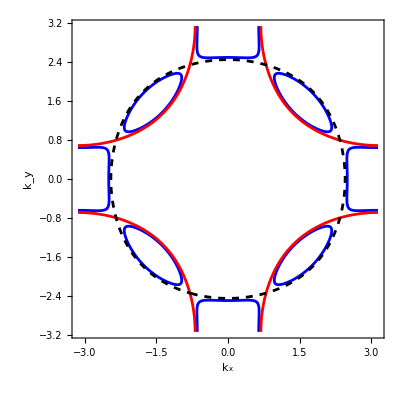

doping p:

0.000278464

ρ_c:

0.499861

ρ_f:

0.499861

General::munfl: 0.9986 1.13260324918×10^-806 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998571 2.14876056493×10^-797 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998479 6.0933255606×10^-770 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

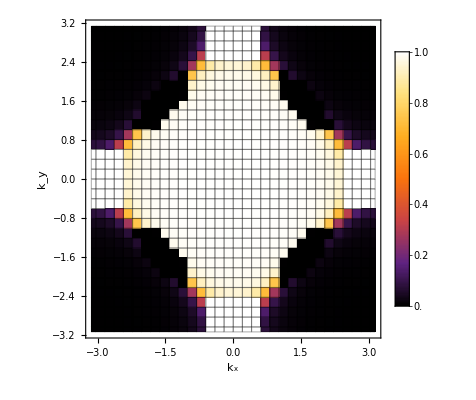

```mathematica
μc=-0.78;
tc=1;
tc1=-0.4;
tc2=0;
tc3=0;
c=4;
L=31;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.3;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;
p=Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]]
(*Export[pathw<>"/fig_FS_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>".pdf",p];*)
T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]


p1=ListDensityPlot[Flatten[Table[{kx,ky,Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>".pdf",p1];*)
```

### p=0.4, t’=-0.2t

#### no order

doping p:

0.374303

ρ_c:

0.312849

ρ_f:

0.312849

General::munfl: 1. 3.1555508456×10^-627 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-880.309] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 4.5887700633×10^-622 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

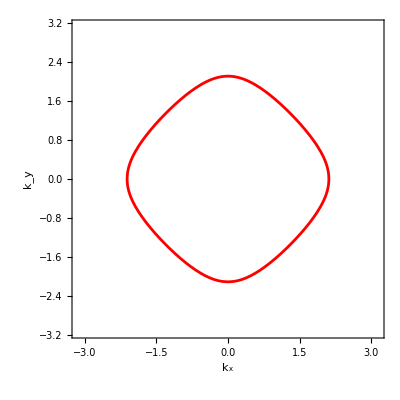
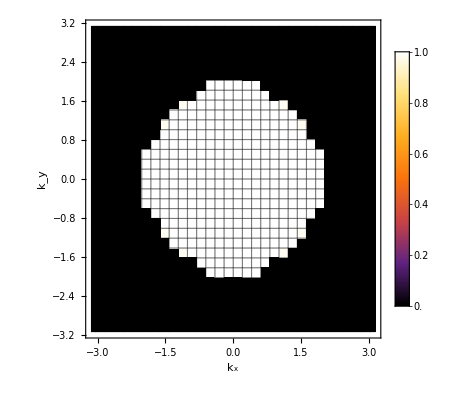

```mathematica
μc=-0.968216901159105;
tc=1;
tc1=-0.0;
tc2=0;
tc3=0;
L=31;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.0;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;
p=Show[ContourPlot[{ekc==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Red},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]];

T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]


p1=ListDensityPlot[Flatten[Table[{kx,ky,Quiet[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic];
{p,p1}
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>"_p="<>ToString[NumberForm[N[1-2ρc],{10,2}]]<>".pdf",p1];
Export[pathw<>"/fig_FS_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_p="<>ToString[NumberForm[N[1-2ρc],{10,2}]]<>".pdf",p];*)
```

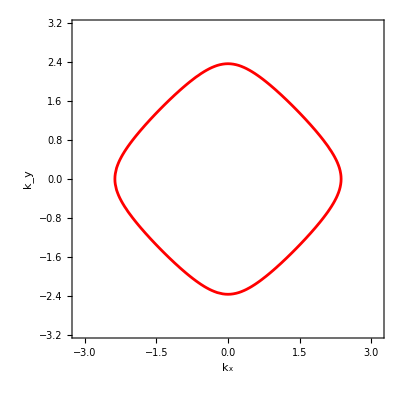
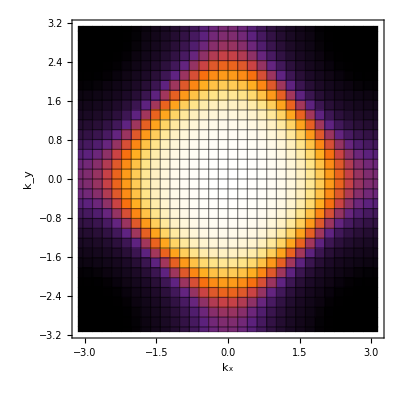
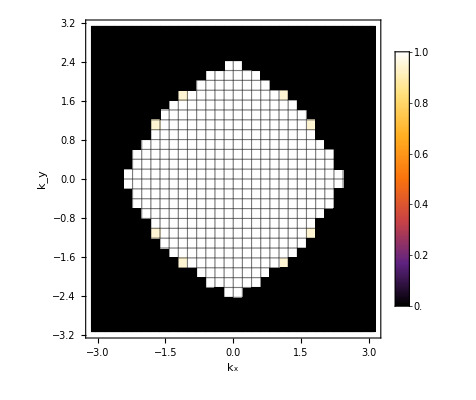

#### AF order

doping p:

0.249941

ρ_c:

0.37503

ρ_f:

0.37503

General::munfl: 0.9986 1.46780799047×10^-587 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-978.171] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998571 2.06387114037×10^-582 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.9986 1.46780799047×10^-587 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-978.171] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998571 2.06387114037×10^-582 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

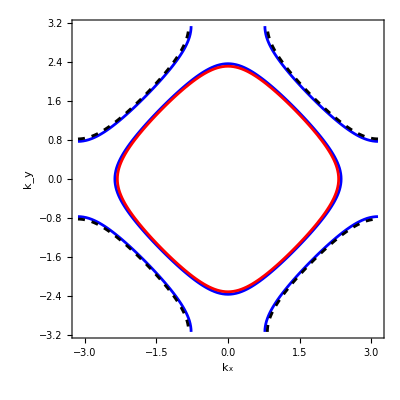
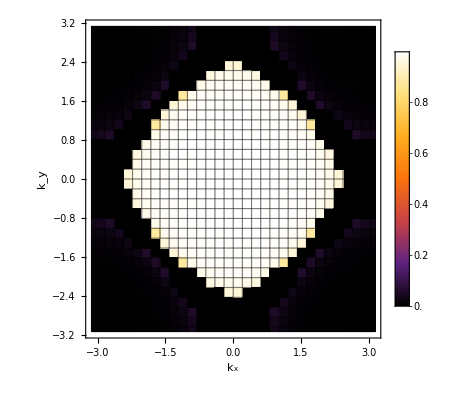
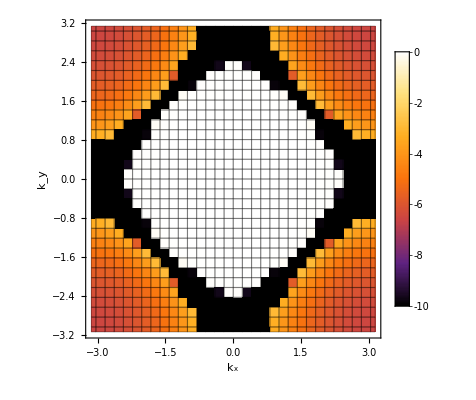

```mathematica
μc=-0.6424145680426989;

tc=1;
tc1=-0.0;
tc2=0;
tc3=0;
c=4;
L=31;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.3;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0.0;
p=Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]];
(*Export[pathw<>"/fig_FS_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_p="<>ToString[NumberForm[N[1-2ρc],{10,2}]]<>".pdf",p];*)
T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]


p1=ListDensityPlot[Flatten[Table[{kx,ky,Quiet[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>"_p="<>ToString[NumberForm[N[1-2ρc],{10,2}]]<>".pdf",p1];*)
p2=ListDensityPlot[Flatten[Table[{kx,ky,Log[Quiet[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",PlotRange->{-10,0},Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_log_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>"_p="<>ToString[NumberForm[N[1-2ρc],{10,2}]]<>".pdf",p2];*)
{p,p1,p2}
```

```mathematica
Plot3D[{E1==enlevel,E2==enlevel,0},{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

#### Kondo metal

doping p:

0.249998

ρ_c:

0.375001

ρ_f:

0.500411

General::munfl: 0.894737 9.93983738154×10^-846 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.893545 4.1067459224×10^-841 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.889911 1.72261853442×10^-827 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.894737 9.93983738154×10^-846 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.893545 4.1067459224×10^-841 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.889911 1.72261853442×10^-827 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

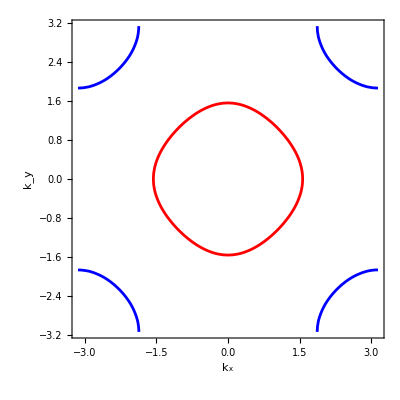
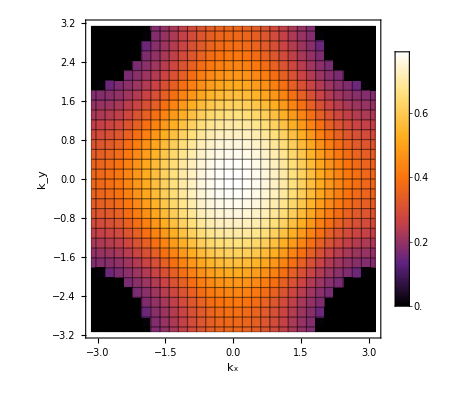
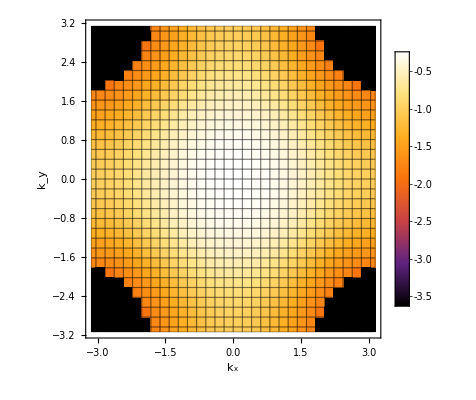

```mathematica
μc=-2.2862705324443864;
μf=-1.08;
tc=1;
tc1=-0.0;
tc2=0;
tc3=0;
c=4;
L=31;

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf;
m=2;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;

p=Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]];
(*Export[pathw<>"/fig_FS_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_L="<>ToString[L]<>"_μf="<>ToString[NumberForm[N[λ],{10,3}]]<>".pdf",p1];*)

T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
p1=ListDensityPlot[Flatten[Table[{kx,ky,Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>"_μf="<>ToString[NumberForm[N[λ],{10,3}]]<>".pdf",p1];*)
p2=ListDensityPlot[Flatten[Table[{kx,ky,Log[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_log_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>"_μf="<>ToString[NumberForm[N[λ],{10,3}]]<>".pdf",p1];*)


{p,p1,p2}
```

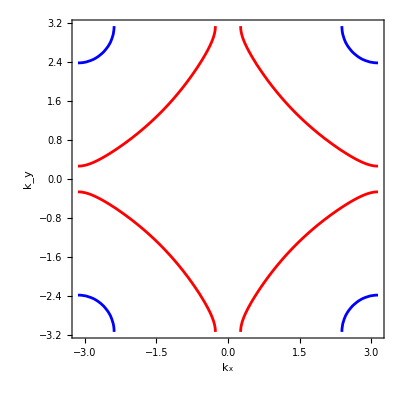
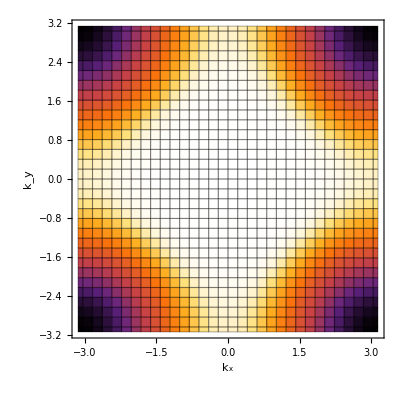
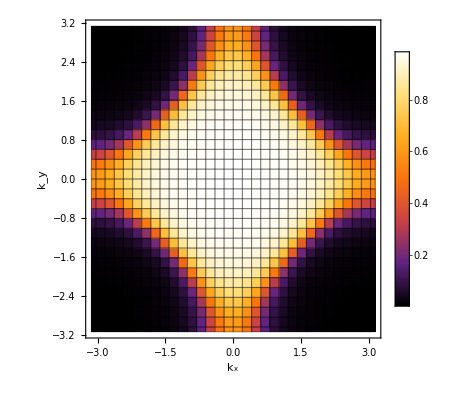
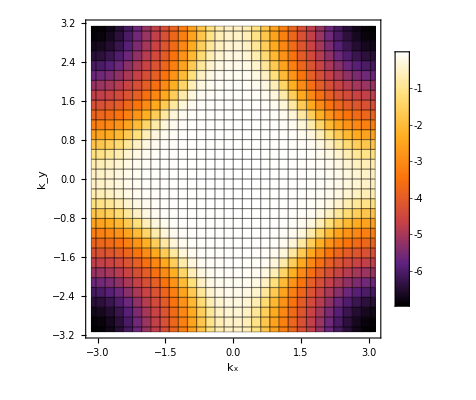

#### Kondo metal with hole pockets

{2.47,-2.47134,-1.20377,-0.00168604,5.99694}

doping p:0.250001

ρ_f = 0.5

Jk = 5.99694

J=0.500024

General::munfl: 0.864493 4.33274497269×10^-940 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.863158 1.25186682718×10^-935 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.859109 1.8047979694×10^-922 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.864493 4.33274497269×10^-940 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.863158 1.25186682718×10^-935 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.859109 1.8047979694×10^-922 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

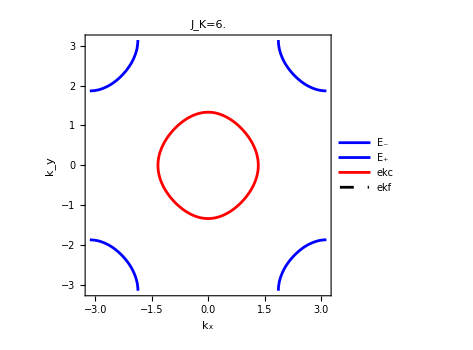
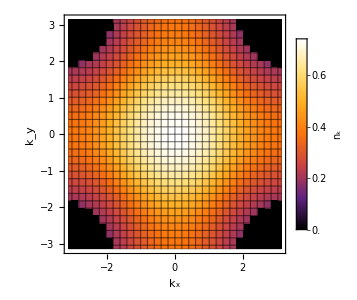
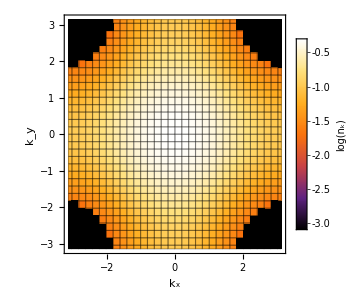

```mathematica
{ϕ,μc,μf,tf,Jk}=list[[123]]

tc=1;

tc1=0.0;
tc2=0;
tc3=0;



ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);


T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);

ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
Print["doping p:", 1-2ρc]


(*Text["ρ_c:"]
ρc*)
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
Print["ρ_f = ",ρf]
Jk=-1/Quiet[NIntegrate[1/(2π)^2((nf[E1]-nf[E2])/(E1-E2)),{kx,-π,π},{ky,-π,π}]];
Print["Jk = ",Jk]
Print["J=",-tf/Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]]

enlevel=0;
p=Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],PlotLegends->{"E_-","E_+","ekc","ekf"},ImageSize->{350,350},AspectRatio->1,MaxRecursion->3],PlotLabel->Style["J_K=" <>ToString[NumberForm[N[Jk,3],3]],Black,20,FontFamily-> "Latin Modern Roman"]];
(*Export[pathw<>"/fig_FS_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>".pdf",p];*)

p1=ListDensityPlot[Flatten[Table[{kx,ky,Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],PlotLegends->BarLegend[Automatic,LegendLabel->"n_k"],ImageSize->{300,300},AspectRatio->1,ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>".pdf",p1];*)


p2=ListDensityPlot[Flatten[Table[{kx,ky,Log[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]},{kx,-π,π,2 π/L},{ky,-π,π,2 π/L}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{300,300},AspectRatio->1,PlotLegends->BarLegend[Automatic,LegendLabel->"log(n_k)"],ClippingStyle->Automatic];
(*Export[pathw<>"/fig_nk_t1="<>ToString[NumberForm[N[tc1],{10,2}]]<>"_m="<>ToString[NumberForm[N[m],{10,2}]]<>"_L="<>ToString[L]<>".pdf",p1];*)

{p,p1,p2}
```

doping p:0.24999

ρ_f = 0.499981

Jk = 1.99603

J=0.499973

General::munfl: 0.989964 1.61240442202×10^-630 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.989792 2.06125012531×10^-625 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.989255 2.62591738643×10^-610 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.989964 1.61240442202×10^-630 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.989792 2.06125012531×10^-625 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.989255 2.62591738643×10^-610 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

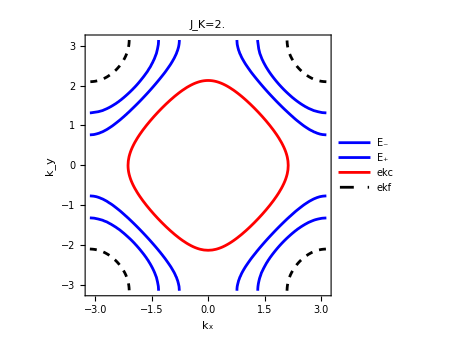
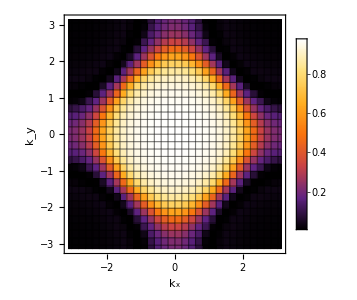
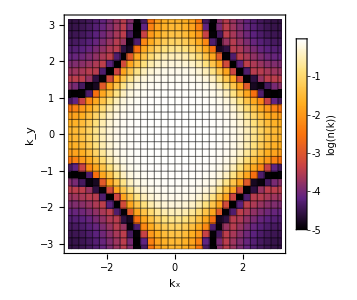

```mathematica
k{0.51,-0.9429697495376651,-0.21301427568415762,0.0709860516300546,1.9960334437666256}
```

```mathematica
NumberForm[Jk,2]
```

1.5

### self-consistent calculation

#### no order

```mathematica
Clear[μc];
(*parameters*)
T=8.61 10^-5 40;

tc=1;
tc1=-0.0;
tc2=0;
tc3=0;

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;

m=0.0;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);

nf[x_]:=1/(1+Exp[x/T]);

(*starting point*)
list={};
μc=-1.6;

p=1/4;

D0=1;
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];

(*initial equations*)
eqn=ρc-(1-p)/2;

While[eqn^2>10^-9,
b=(- eqn)/D0;
(*update solutions*)
μc+=b;

ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];

eqnnew=ρc-(1-p)/2;
(*update matrix*)

D0=(eqnnew-eqn)/b;
eqn=eqnnew;
]
Text["Solution"]
μc
```

Solution

-0.568217

#### AF order

```mathematica
Clear[μc];
(*parameters*)
T=8.61 10^-5 40;

tc=1;
tc1=-0.0;
tc2=0;
tc3=0;

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;

m=0.3;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);

nf[x_]:=1/(1+Exp[x/T]);

(*starting point*)
list={};
μc=-1.6;

p=0.25;

D0=1;
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];

(*initial equations*)
eqn=ρc-(1-p)/2;

While[eqn^2>10^-9,
b=(- eqn)/D0;
(*update solutions*)
μc+=b;

ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];

eqnnew=ρc-(1-p)/2;
(*update matrix*)

D0=(eqnnew-eqn)/b;
eqn=eqnnew;
]
Text["Solution"]
μc
```

Solution

-0.642415

#### Kondo order

```mathematica
{μc,μf,tf}={-2.024490930039162,-0.877906078060167,0.0034494782114981937};
tc=1;

tc1=0.0;
tc2=0;
tc3=0;


ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);
m=2;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
```

```mathematica
list={};


p=1/4;
D0=IdentityMatrix[2];
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
(*initial equations*)
eqn={ρc-(1-p)/2,ρf-1/2};

While[eqn.eqn>10^-9,
b=-Inverse[N[D0]].eqn;
(*update solutions*)
μc+=b[[1]];
μf+=b[[2]];

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
eqn={ρc-(1-p)/2,ρf-1/2};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
];

μcold=μc
μfold=μf
```

-2.02449

-0.877906

```mathematica
-1/Quiet[NIntegrate[1/(2π)^2((nf[E1]-nf[E2])/(E1-E2)),{kx,-π,π},{ky,-π,π}]]
```

4.97155

```mathematica
Q=-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

0.00721351 J

```mathematica
-tf/Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

0.147767

```mathematica
-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

0.00770881 J

#### full self consistently

```mathematica
μc=-2;
μf=-1;
tf=0.001;



ϕ=2;
p=1./4;
J=0.5;
tc=1;
tc1=0.0;
tc2=0;
tc3=0;


T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);

D0=IdentityMatrix[3];
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
tfn=-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
(*initial equations*)
eqn={ρc-(1-p)/2,ρf-1/2,tfn-tf};
```

```mathematica
eqn
```

{0.0018884,-0.0607852,-0.0104598}

```mathematica
While[eqn.eqn>10^-9,
b=-Inverse[N[D0]].eqn;
(*update solutions*)
μc+=b[[1]];
μf+=b[[2]];
tf+=b[[3]];

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
tfn=-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
eqn={ρc-(1-p)/2,ρf-1/2,tfn-tf};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
];
Jk=-1/Quiet[NIntegrate[1/(2π)^2((nf[E1]-nf[E2])/(E1-E2)),{kx,-π,π},{ky,-π,π}]];
Print["μc= ",μc, " μf = ", μf, " tf = ", tf , " Jk = ", Jk]
{μc,μf,tf}
```

μc= -2.02449 μf = -0.877906 tf = 0.00344948 Jk = 4.96765

{-2.02449,-0.877906,0.00344948}

#### continuus transition

```mathematica
list={};
{ϕ,μc,μf,tf,Jk}={0.65,-1.0380288324995022,-0.2535428025748895,0.054374222689623095,2.223042929410955};
Do[
p=1./4;
J=0.5;
tc=1;
tc1=0.0;
tc2=0;
tc3=0;


T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);

D0=IdentityMatrix[3];
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
tfn=-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
(*initial equations*)
eqn={ρc-(1-p)/2,ρf-1/2,tfn-tf};
While[eqn.eqn>10^-9,
b=-Inverse[N[D0]].eqn;
(*update solutions*)
μc+=b[[1]];
μf+=b[[2]];
tf+=b[[3]];

ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
tfn=-J Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
eqn={ρc-(1-p)/2,ρf-1/2,tfn-tf};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
];
Jk=-1/Quiet[NIntegrate[1/(2π)^2((nf[E1]-nf[E2])/(E1-E2)),{kx,-π,π},{ky,-π,π}]];
AppendTo[list,{ϕ,μc,μf,tf,Jk}];
Print[{ϕ,μc,μf,tf,Jk}];
,{ϕ,0.65,3,0.02}]
```

```mathematica
list
```

```mathematica
list={{0.01,-0.5686706530538096,-0.0002491399661287969,0.10122991059635923,1.1958861595906274},{0.03,-0.5721549439188858,-0.0022134293060832554,0.10103869693705883,1.2037174214288955},{0.05,-0.5787854844716642,-0.006002800953325085,0.10065793453047504,1.2186622703347754},{0.06999999999999999,-0.5881879973514923,-0.011392453184591643,0.10015969037752875,1.2399976832640696},{0.09,-0.5994450486412438,-0.018116140894172204,0.09946352000642739,1.2657732975477543},{0.11,-0.6125024303906771,-0.02590383523131562,0.09871404217387804,1.295843463352467},{0.13,-0.6265505629066456,-0.0345074354292577,0.09787496120233827,1.3287290327262091},{0.15000000000000002,-0.641310781140504,-0.04369815852531737,0.0969718199494533,1.3636410087804693},{0.17,-0.6565927237966906,-0.053293208518135446,0.0960194625122415,1.3998712596807767},{0.19,-0.6722563438358408,-0.06316003610495684,0.09502199275144883,1.4368222649161402},{0.21000000000000002,-0.6882473965186312,-0.07320249073004574,0.09397992368129718,1.4740386378153771},{0.23,-0.70455872644396,-0.08335053771147156,0.09289004936630188,1.5111593530667409},{0.25,-0.721293761234755,-0.09355023067268674,0.09173765543639807,1.5480810035378452},{0.27,-0.7383613957947986,-0.10376100395879535,0.09051974025537157,1.584361515656275},{0.29000000000000004,-0.7558459534969106,-0.11393657691604048,0.0892227211317237,1.6199189391265574},{0.31,-0.7737149322139706,-0.12402745671721405,0.08783525716131156,1.6547390023235924},{0.33,-0.7918395747768064,-0.13397318671160172,0.0863642894685785,1.688966162313405},{0.35000000000000003,-0.8099528834574797,-0.14372160313296622,0.0848265634963255,1.722943918333918},{0.37,-0.8278106651079901,-0.15324408980185775,0.08324514340314834,1.7569813660315203},{0.39,-0.8452982354581885,-0.16252997288194304,0.08162905797897677,1.7911041334907614},{0.41000000000000003,-0.8624461086787759,-0.17159710204688763,0.07999360841090583,1.825500169348359},{0.43,-0.8791894401365521,-0.18041232712158758,0.07829206263194431,1.8597816592020477},{0.45,-0.8956165191949584,-0.18897783529279766,0.07654310563050866,1.8940390776805762},{0.47000000000000003,-0.9117568651251745,-0.19729125975021494,0.07476331321945917,1.9282033781744143},{0.49,-0.9275523615235056,-0.20531097659629258,0.07291120701202379,1.9622157444896788},{0.51,-0.9429697495376651,-0.21301427568415762,0.0709860516300546,1.9960334437666256},{0.53,-0.958143983293069,-0.22038742270969805,0.06901359454530699,2.0296195745250976},{0.55,-0.9727875895106268,-0.22734323813379215,0.0669137076342934,2.062950178374266},{0.5700000000000001,-0.9870621135468032,-0.23386583351376364,0.06472865052549708,2.095944669345006},{0.59,-1.00082185670021,-0.23987415830354228,0.062420667548329284,2.1285554967758467},{0.61,-1.0140027549562138,-0.24526123320977597,0.059955423785120636,2.1607143664163604},{0.65,-1.0380288324995022,-0.2535428025748895,0.054374222689623095,2.223042929410955},{0.67,-1.0483515459913872,-0.2558291789067949,0.05107027050609419,2.252612377996679},{0.6900000000000001,-1.0567204712192924,-0.2559484483628863,0.04712566862757777,2.280222440278755},{0.71,-1.0610832192425916,-0.2516435160138696,0.04180934031568246,2.3038311608165576},{0.73,-1.0579620242484042,-0.23975568642436493,0.03442615499303758,2.322143034861987},{0.75,-1.061516060775902,-0.2366793084349285,0.030728154059413905,2.3531461658117485},{0.77,-1.0700310017067778,-0.23923580531564548,0.0289651164049338,2.3901186312073315},{0.79,-1.0802532979400485,-0.24378122548293762,0.027810699679823695,2.428840829116651},{0.81,-1.091497634483285,-0.24935083478316078,0.02693250908726203,2.468429341088545},{0.8300000000000001,-1.1031588619079107,-0.25554439642410703,0.02619442627540722,2.5084481764839115},{0.8500000000000001,-1.115029137908713,-0.26216795027087253,0.02553868945626273,2.5486441809354656},{0.87,-1.1276080580041818,-0.26908797213742724,0.024926724100620266,2.5891460635003596},{0.89,-1.1401562505130882,-0.2762833135787406,0.024349040627606885,2.629701446665748},{0.91,-1.1529087835754144,-0.2836981711366266,0.02379308498110283,2.6703380402213837},{0.93,-1.1658319712804368,-0.2913143385391406,0.023254851582775578,2.711038725467959},{0.95,-1.178958963865775,-0.29909314487554095,0.022714725491150955,2.7518919612537815},{0.97,-1.1921074862463246,-0.30710552116024026,0.022217340071230267,2.792656691844307},{0.99,-1.205555907545886,-0.3152260601706169,0.02170216153799373,2.833588934044982},{1.01,-1.2190603461981955,-0.3235386182725758,0.02121297130045068,2.874492834624227},{1.03,-1.232716560675752,-0.3319759372233996,0.02070863771531798,2.9155616629302794},{1.05,-1.246640092350338,-0.3405969840114759,0.020237223796216,2.9566233328776326},{1.07,-1.2604356075333925,-0.3493463077848522,0.019753855913917356,2.99773236053952},{1.09,-1.2744771344769228,-0.35825543040353797,0.019290570669721133,3.038882135527059},{1.11,-1.288624036453298,-0.3672995003068049,0.018827729367159016,3.08010844889415},{1.13,-1.302952343657188,-0.3764785208178121,0.01837162360692903,3.121399104073197},{1.15,-1.3173726118979887,-0.38579501172400227,0.017921539743978986,3.16273934085746},{1.17,-1.3319321312556094,-0.3952507438032561,0.01748390912335484,3.204112331886634},{1.19,-1.3465845461184662,-0.404827891669981,0.017043242457695198,3.2455713541893867},{1.21,-1.3613690643620295,-0.4145339904964411,0.01661019907129752,3.287081093361886},{1.23,-1.3762750731991402,-0.4243649719208941,0.0161826852883644,3.328650099358101},{1.25,-1.3912452983365733,-0.4343424671003355,0.01577811736610282,3.370191268600537},{1.27,-1.4065251907050695,-0.4443653396142899,0.015324517772909302,3.412050134925207},{1.29,-1.421752688151669,-0.45456582907179394,0.014918595180739734,3.45375926519687},{1.31,-1.4370935725453649,-0.4648817447249853,0.014517505103250998,3.4955264211441706},{1.33,-1.4525444369988858,-0.4753117281009073,0.014121824440511799,3.537348234326439},{1.35,-1.4680947879137978,-0.4858487106902773,0.013727091828406503,3.579236479111538},{1.37,-1.4837175939304699,-0.4965224993770291,0.01335857216934352,3.6210955489030643},{1.3900000000000001,-1.4995118372078788,-0.5072812718704907,0.01297856205604706,3.663088892000442},{1.4100000000000001,-1.5154458659485137,-0.5181255486656832,0.012587936724460859,3.7052016951068585},{1.4300000000000002,-1.5314363973632454,-0.5290916239636606,0.012215603228466737,3.747306903072451},{1.4500000000000002,-1.5475196883852183,-0.5401847493209134,0.011867110335852025,3.7894052734749173},{1.4700000000000002,-1.5637628302569013,-0.5513184450027593,0.011480335253469887,3.8317072427347023},{1.49,-1.5801274224320383,-0.5626164163286481,0.011146442138100659,3.8739375958775026},{1.51,-1.5964678810839426,-0.5739645366103713,0.010786025054371894,3.9162416130006994},{1.53,-1.6128841374166694,-0.5854059787754126,0.010421829282965393,3.9586362277830216},{1.55,-1.629515831376795,-0.5969614297068018,0.010086878586132853,4.001041553203228},{1.57,-1.6462086563985614,-0.6086048015997724,0.009749263349736189,4.043519106723884},{1.59,-1.6630321539374096,-0.6203280715081092,0.009409876158333195,4.08608145752204},{1.6099999999999999,-1.679785927015067,-0.6321504383720705,0.009081046380549657,4.128604051980059},{1.63,-1.6966665439104778,-0.6440456677920169,0.008745538987190434,4.171228643589108},{1.65,-1.7137011824461892,-0.6560302372774095,0.008421444556179193,4.213904552072793},{1.67,-1.7308560723141453,-0.6680905809899785,0.008098003023373233,4.256650670823907},{1.69,-1.7480494771693877,-0.6802440691954514,0.007786805236348071,4.299401209838766},{1.71,-1.765390810819706,-0.6924493768387616,0.007463053220976405,4.342264444556786},{1.73,-1.7827104232122104,-0.7047789178870891,0.007169397190101269,4.385075457227636},{1.75,-1.8001057206574074,-0.7171792341381938,0.006878639547415093,4.427921757838918},{1.77,-1.8176368656934716,-0.7296099039924887,0.006587904760137021,4.470761484918779},{1.79,-1.8352536512061084,-0.7421514310284358,0.006292927708512476,4.513783322013597},{1.81,-1.852963846439616,-0.7547723566593934,0.005996080979650973,4.556906406005916},{1.83,-1.8705973930906465,-0.7674648824264378,0.005718384556255491,4.59990233388399},{1.85,-1.8884534888350952,-0.7801997815749235,0.005423509944971765,4.643078780531},{1.87,-1.9062505142929642,-0.7930352624970585,0.005164177315414562,4.686114765303757},{1.8900000000000001,-1.9241004220106666,-0.8059519507304552,0.00491243762779463,4.729190123759946},{1.9100000000000001,-1.9422323411739268,-0.8188714944863864,0.00462175165268782,4.77252397950913},{1.9300000000000002,-1.9603557136512995,-0.8318803371959335,0.004351459144399124,4.81581405855182},{1.9500000000000002,-1.9785362017169632,-0.8449554082252337,0.004086701712815407,4.8591319283751595},{1.9700000000000002,-1.9967766802257843,-0.8580940308143731,0.003826357538484631,4.902481861480395},{1.9900000000000002,-2.015080315468247,-0.8712941601534739,0.003569755997899685,4.945867137599147},{2.0100000000000002,-2.033446759924071,-0.8845544336410113,0.003316685548659401,4.989288183110934},{2.0300000000000002,-2.0518756942639755,-0.8978736286243236,0.0030670195583404765,5.03274501065538},{2.0500000000000003,-2.070366161973339,-0.9112506072407957,0.0028206742294807083,5.076236972790158},{2.07,-2.088912944567902,-0.9246848392703362,0.0025779079257233677,5.119760894323355},{2.09,-2.107526404158373,-0.9381738508331281,0.00233782596896376,5.16332434197691},{2.11,-2.1261991843726755,-0.9517171805362162,0.002100766744619833,5.206922090925146},{2.13,-2.144927050768657,-0.9653144951728446,0.0018670109750980016,5.250551325286262},{2.15,-2.1637118622636637,-0.9789643802199613,0.0016362817616599073,5.294213549555836},{2.17,-2.182552877998093,-0.9926658219990022,0.0014085053357737742,5.337908284654693},{2.19,-2.2014488383556996,-1.0064179349944178,0.0011836626447607381,5.381635253817489},{2.21,-2.2203992867543945,-1.0202197101502417,0.0009616684205984311,5.425393854286694},{2.23,-2.2394878279515136,-1.0340521816781674,0.0007318959538430398,5.469257336878978},{2.25,-2.258462541326056,-1.0479683517384557,0.0005258470947649632,5.513006379317347},{2.27,-2.277560406827113,-1.0619111833853823,0.00031182921513323936,5.5568463514356035},{2.29,-2.2967294470283655,-1.0759035499227698,0.00010065992283577851,5.600735856017385},{2.31,-2.3159410145106043,-1.0899400898183036,-0.00010788944766161384,5.644647325663649},{2.33,-2.3352008844797054,-1.1040210306328146,-0.00031382097055188205,5.688586685390766},{2.35,-2.3545078911107598,-1.1181456412007034,-0.0005171565505769088,5.73255327912455},{2.37,-2.373860397970084,-1.1323131360035736,-0.0007179412620783631,5.776546095844872},{2.39,-2.393236153698986,-1.1465221178749416,-0.0009156811863567302,5.820545627860589},{2.41,-2.412744053538591,-1.1607746622636574,-0.0011129289194669713,5.864646867440205},{2.43,-2.432222967538086,-1.1750659172526619,-0.001306114416572473,5.908710184775932},{2.45,-2.4517592532752466,-1.189397419562115,-0.0014972241678519547,5.952810815224007},{2.47,-2.471340694910208,-1.203768163548969,-0.0016860380701682342,5.996938291244174},{2.49,-2.4909659652705716,-1.2181774227268782,-0.0018725794169938829,6.041091730523094},{2.5100000000000002,-2.5106339580256276,-1.2326245097479764,-0.002056875465327903,6.08527031986294},{2.5300000000000002,-2.5303438753245313,-1.2471087609236167,-0.002238958346969725,6.129473590346203},{2.5500000000000003,-2.5500950184496793,-1.261629517052471,-0.002418862479137917,6.173701577987975},{2.57,-2.5698866507754716,-1.2761861619692931,-0.0025966211408836185,6.21795251289005},{2.59,-2.5897173211428286,-1.2907781675303007,-0.0027722246651804877,6.262226760139157},{2.61,-2.6095887328855465,-1.3054045854372052,-0.002945830242506819,6.306526421017768},{2.63,-2.6294980242079293,-1.3200651321142733,-0.0031173491955256375,6.350845903571052},{2.65,-2.649444837289207,-1.3347591302647352,-0.0032868317272030834,6.39518841603958},{2.67,-2.66942962736653,-1.3494860624422482,-0.0034543670630370715,6.43955375929394},{2.69,-2.68945077447817,-1.3642452360895574,-0.0036199216669791094,6.483940202376509},{2.71,-2.7095085080116066,-1.3790362315330063,-0.003783579468304684,6.52834857040767},{2.73,-2.7296014558171486,-1.3938584388982558,-0.003945324370516261,6.57277751305014},{2.75,-2.7497294560985486,-1.4087113445968138,-0.00410520609423267,6.6172271475402145},{2.77,-2.7698917035579473,-1.4235944369824993,-0.004263239000968435,6.661696929597062},{2.79,-2.7900884824176466,-1.4385071296801544,-0.004419490916978346,6.706187182886158},{2.81,-2.8103180031650314,-1.4534491097119702,-0.004573943645180712,6.750696786483896},{2.83,-2.8305805253686316,-1.4684197353779929,-0.004726643419443954,6.795225789809965},{2.85,-2.850875375258273,-1.4834185749375606,-0.004877616105857685,6.839773901894244},{2.87,-2.8712019260005563,-1.498445163864586,-0.00502688337750533,6.884340693100397},{2.89,-2.8915603259814673,-1.5134984077414098,-0.0051748142549546015,6.928926940118043},{2.91,-2.9119472669308646,-1.5285795984782002,-0.005320346135793912,6.973527722053409},{2.93,-2.932368170072128,-1.5436867192649768,-0.0054647415775632485,7.0181511147108075},{2.95,-2.9528180052113604,-1.5588198013068884,-0.005607494376373062,7.062791136504342},{2.9699999999999998,-2.973296830495425,-1.5739783908147111,-0.005748646963982105,7.107447955789938},{2.9899999999999998,-2.9938045713653287,-1.5891621065621961,-0.005888243725271259,7.152120953645757}}
```

{{0.01,-0.568671,-0.00024914,0.10123,1.19589},{0.03,-0.572155,-0.00221343,0.101039,1.20372},{0.05,-0.578785,-0.0060028,0.100658,1.21866},{0.07,-0.588188,-0.0113925,0.10016,1.24},{0.09,-0.599445,-0.0181161,0.0994635,1.26577},{0.11,-0.612502,-0.0259038,0.098714,1.29584},{0.13,-0.626551,-0.0345074,0.097875,1.32873},{0.15,-0.641311,-0.0436982,0.0969718,1.36364},{0.17,-0.656593,-0.0532932,0.0960195,1.39987},{0.19,-0.672256,-0.06316,0.095022,1.43682},{0.21,-0.688247,-0.0732025,0.0939799,1.47404},{0.23,-0.704559,-0.0833505,0.09289,1.51116},{0.25,-0.721294,-0.0935502,0.0917377,1.54808},{0.27,-0.738361,-0.103761,0.0905197,1.58436},{0.29,-0.755846,-0.113937,0.0892227,1.61992},{0.31,-0.773715,-0.124027,0.0878353,1.65474},{0.33,-0.79184,-0.133973,0.0863643,1.68897},{0.35,-0.809953,-0.143722,0.0848266,1.72294},{0.37,-0.827811,-0.153244,0.0832451,1.75698},{0.39,-0.845298,-0.16253,0.0816291,1.7911},{0.41,-0.862446,-0.171597,0.0799936,1.8255},{0.43,-0.879189,-0.180412,0.0782921,1.85978},{0.45,-0.895617,-0.188978,0.0765431,1.89404},{0.47,-0.911757,-0.197291,0.0747633,1.9282},{0.49,-0.927552,-0.205311,0.0729112,1.96222},{0.51,-0.94297,-0.213014,0.0709861,1.99603},{0.53,-0.958144,-0.220387,0.0690136,2.02962},{0.55,-0.972788,-0.227343,0.0669137,2.06295},{0.57,-0.987062,-0.233866,0.0647287,2.09594},{0.59,-1.00082,-0.239874,0.0624207,2.12856},{0.61,-1.014,-0.245261,0.0599554,2.16071},{0.65,-1.03803,-0.253543,0.0543742,2.22304},{0.67,-1.04835,-0.255829,0.0510703,2.25261},{0.69,-1.05672,-0.255948,0.0471257,2.28022},{0.71,-1.06108,-0.251644,0.0418093,2.30383},{0.73,-1.05796,-0.239756,0.0344262,2.32214},{0.75,-1.06152,-0.236679,0.0307282,2.35315},{0.77,-1.07003,-0.239236,0.0289651,2.39012},{0.79,-1.08025,-0.243781,0.0278107,2.42884},{0.81,-1.0915,-0.249351,0.0269325,2.46843},{0.83,-1.10316,-0.255544,0.0261944,2.50845},{0.85,-1.11503,-0.262168,0.0255387,2.54864},{0.87,-1.12761,-0.269088,0.0249267,2.58915},{0.89,-1.14016,-0.276283,0.024349,2.6297},{0.91,-1.15291,-0.283698,0.0237931,2.67034},{0.93,-1.16583,-0.291314,0.0232549,2.71104},{0.95,-1.17896,-0.299093,0.0227147,2.75189},{0.97,-1.19211,-0.307106,0.0222173,2.79266},{0.99,-1.20556,-0.315226,0.0217022,2.83359},{1.01,-1.21906,-0.323539,0.021213,2.87449},{1.03,-1.23272,-0.331976,0.0207086,2.91556},{1.05,-1.24664,-0.340597,0.0202372,2.95662},{1.07,-1.26044,-0.349346,0.0197539,2.99773},{1.09,-1.27448,-0.358255,0.0192906,3.03888},{1.11,-1.28862,-0.3673,0.0188277,3.08011},{1.13,-1.30295,-0.376479,0.0183716,3.1214},{1.15,-1.31737,-0.385795,0.0179215,3.16274},{1.17,-1.33193,-0.395251,0.0174839,3.20411},{1.19,-1.34658,-0.404828,0.0170432,3.24557},{1.21,-1.36137,-0.414534,0.0166102,3.28708},{1.23,-1.37628,-0.424365,0.0161827,3.32865},{1.25,-1.39125,-0.434342,0.0157781,3.37019},{1.27,-1.40653,-0.444365,0.0153245,3.41205},{1.29,-1.42175,-0.454566,0.0149186,3.45376},{1.31,-1.43709,-0.464882,0.0145175,3.49553},{1.33,-1.45254,-0.475312,0.0141218,3.53735},{1.35,-1.46809,-0.485849,0.0137271,3.57924},{1.37,-1.48372,-0.496522,0.0133586,3.6211},{1.39,-1.49951,-0.507281,0.0129786,3.66309},{1.41,-1.51545,-0.518126,0.0125879,3.7052},{1.43,-1.53144,-0.529092,0.0122156,3.74731},{1.45,-1.54752,-0.540185,0.0118671,3.78941},{1.47,-1.56376,-0.551318,0.0114803,3.83171},{1.49,-1.58013,-0.562616,0.0111464,3.87394},{1.51,-1.59647,-0.573965,0.010786,3.91624},{1.53,-1.61288,-0.585406,0.0104218,3.95864},{1.55,-1.62952,-0.596961,0.0100869,4.00104},{1.57,-1.64621,-0.608605,0.00974926,4.04352},{1.59,-1.66303,-0.620328,0.00940988,4.08608},{1.61,-1.67979,-0.63215,0.00908105,4.1286},{1.63,-1.69667,-0.644046,0.00874554,4.17123},{1.65,-1.7137,-0.65603,0.00842144,4.2139},{1.67,-1.73086,-0.668091,0.008098,4.25665},{1.69,-1.74805,-0.680244,0.00778681,4.2994},{1.71,-1.76539,-0.692449,0.00746305,4.34226},{1.73,-1.78271,-0.704779,0.0071694,4.38508},{1.75,-1.80011,-0.717179,0.00687864,4.42792},{1.77,-1.81764,-0.72961,0.0065879,4.47076},{1.79,-1.83525,-0.742151,0.00629293,4.51378},{1.81,-1.85296,-0.754772,0.00599608,4.55691},{1.83,-1.8706,-0.767465,0.00571838,4.5999},{1.85,-1.88845,-0.7802,0.00542351,4.64308},{1.87,-1.90625,-0.793035,0.00516418,4.68611},{1.89,-1.9241,-0.805952,0.00491244,4.72919},{1.91,-1.94223,-0.818871,0.00462175,4.77252},{1.93,-1.96036,-0.83188,0.00435146,4.81581},{1.95,-1.97854,-0.844955,0.0040867,4.85913},{1.97,-1.99678,-0.858094,0.00382636,4.90248},{1.99,-2.01508,-0.871294,0.00356976,4.94587},{2.01,-2.03345,-0.884554,0.00331669,4.98929},{2.03,-2.05188,-0.897874,0.00306702,5.03275},{2.05,-2.07037,-0.911251,0.00282067,5.07624},{2.07,-2.08891,-0.924685,0.00257791,5.11976},{2.09,-2.10753,-0.938174,0.00233783,5.16332},{2.11,-2.1262,-0.951717,0.00210077,5.20692},{2.13,-2.14493,-0.965314,0.00186701,5.25055},{2.15,-2.16371,-0.978964,0.00163628,5.29421},{2.17,-2.18255,-0.992666,0.00140851,5.33791},{2.19,-2.20145,-1.00642,0.00118366,5.38164},{2.21,-2.2204,-1.02022,0.000961668,5.42539},{2.23,-2.23949,-1.03405,0.000731896,5.46926},{2.25,-2.25846,-1.04797,0.000525847,5.51301},{2.27,-2.27756,-1.06191,0.000311829,5.55685},{2.29,-2.29673,-1.0759,0.00010066,5.60074},{2.31,-2.31594,-1.08994,-0.000107889,5.64465},{2.33,-2.3352,-1.10402,-0.000313821,5.68859},{2.35,-2.35451,-1.11815,-0.000517157,5.73255},{2.37,-2.37386,-1.13231,-0.000717941,5.77655},{2.39,-2.39324,-1.14652,-0.000915681,5.82055},{2.41,-2.41274,-1.16077,-0.00111293,5.86465},{2.43,-2.43222,-1.17507,-0.00130611,5.90871},{2.45,-2.45176,-1.1894,-0.00149722,5.95281},{2.47,-2.47134,-1.20377,-0.00168604,5.99694},{2.49,-2.49097,-1.21818,-0.00187258,6.04109},{2.51,-2.51063,-1.23262,-0.00205688,6.08527},{2.53,-2.53034,-1.24711,-0.00223896,6.12947},{2.55,-2.5501,-1.26163,-0.00241886,6.1737},{2.57,-2.56989,-1.27619,-0.00259662,6.21795},{2.59,-2.58972,-1.29078,-0.00277222,6.26223},{2.61,-2.60959,-1.3054,-0.00294583,6.30653},{2.63,-2.6295,-1.32007,-0.00311735,6.35085},{2.65,-2.64944,-1.33476,-0.00328683,6.39519},{2.67,-2.66943,-1.34949,-0.00345437,6.43955},{2.69,-2.68945,-1.36425,-0.00361992,6.48394},{2.71,-2.70951,-1.37904,-0.00378358,6.52835},{2.73,-2.7296,-1.39386,-0.00394532,6.57278},{2.75,-2.74973,-1.40871,-0.00410521,6.61723},{2.77,-2.76989,-1.42359,-0.00426324,6.6617},{2.79,-2.79009,-1.43851,-0.00441949,6.70619},{2.81,-2.81032,-1.45345,-0.00457394,6.7507},{2.83,-2.83058,-1.46842,-0.00472664,6.79523},{2.85,-2.85088,-1.48342,-0.00487762,6.83977},{2.87,-2.8712,-1.49845,-0.00502688,6.88434},{2.89,-2.89156,-1.5135,-0.00517481,6.92893},{2.91,-2.91195,-1.52858,-0.00532035,6.97353},{2.93,-2.93237,-1.54369,-0.00546474,7.01815},{2.95,-2.95282,-1.55882,-0.00560749,7.06279},{2.97,-2.9733,-1.57398,-0.00574865,7.10745},{2.99,-2.9938,-1.58916,-0.00588824,7.15212}}

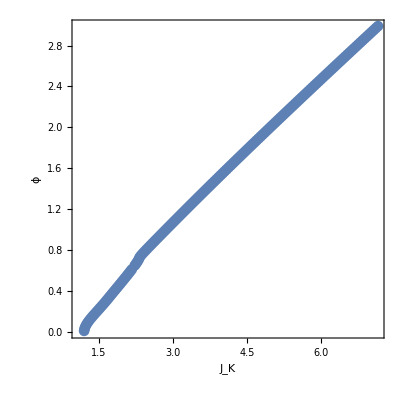

```mathematica
ListPlot[Table[{list[[i]][[5]],list[[i]][[1]]},{i,1,Dimensions[list][[1]]}],PlotMarkers->Automatic,Joined->True,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J_K","ϕ"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

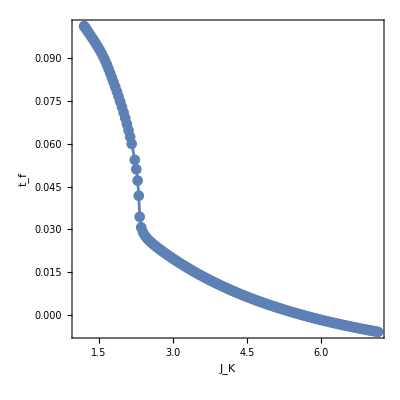

```mathematica
ListPlot[Table[{list[[i]][[5]],list[[i]][[4]]},{i,1,Dimensions[list][[1]]}],PlotMarkers->Automatic,Joined->True,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J_K","t_f"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

#### results

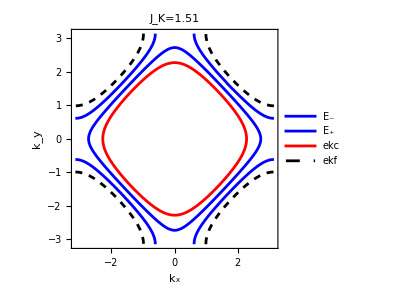
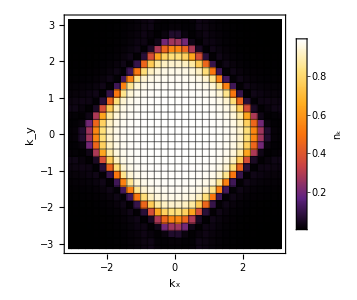
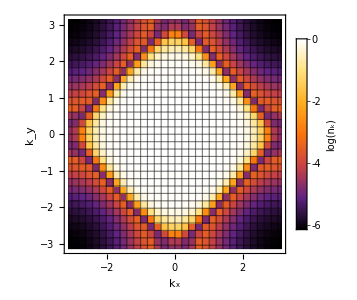

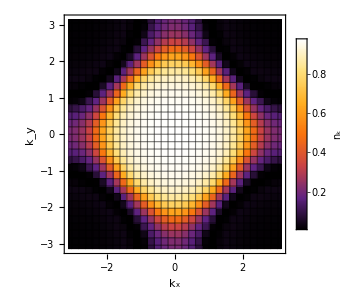
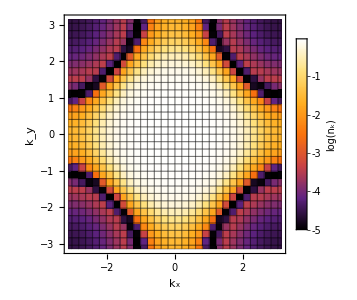
```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

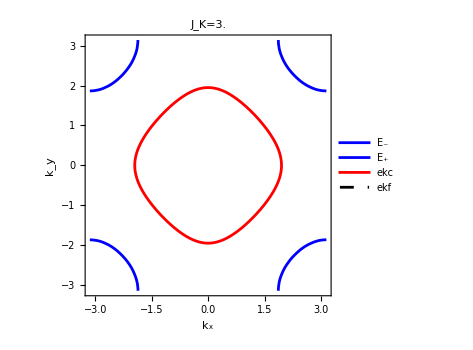
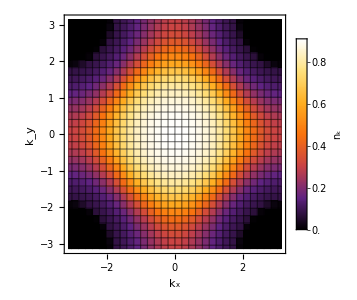
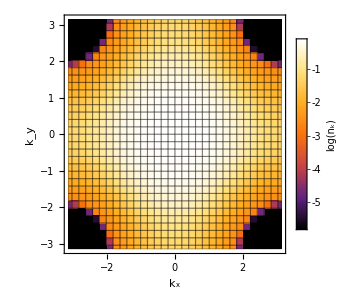

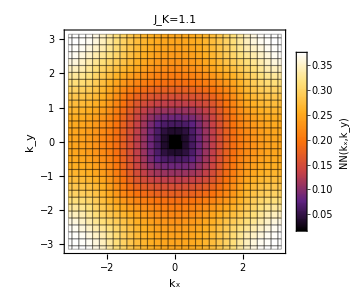
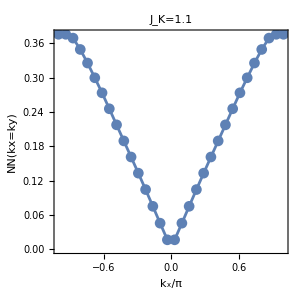

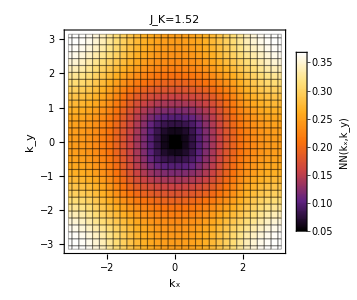
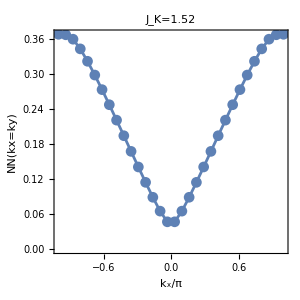

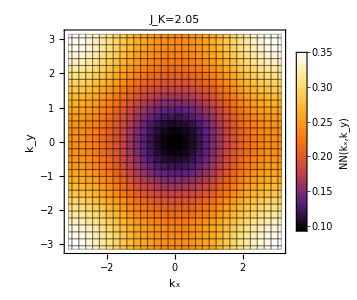

### density-density response function

```mathematica
Clear[qx,qy];
{ϕ,μc,μf,tf,Jk}=list[[123]]

tc=1;

tc1=0.0;
tc2=0;
tc3=0;
L=31;



ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=-μf+2 tf(Cos[kx]+Cos[ky]);

(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+ϕ^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+ϕ^2);


T=8.61 10^-5 240;
nf[x_]:=1/(1+Exp[x/T]);
nb[x_]:=1/(-1+Exp[x/T]);

ekcq=ekc/.kx->kx+qx/.ky->ky+qy;
ekfq=ekf/.kx->kx+qx/.ky->ky+qy;
E1q=(ekcq+ekfq)/2+√(((ekcq-ekfq)/2)^2+ϕ^2);
E2q=(ekcq+ekfq)/2-√(((ekcq-ekfq)/2)^2+ϕ^2);
u1=(E1-ekf)/(E1-E2);
u2=(E2-ekf)/(E2-E1);
u1q=(E1q-ekfq)/(E1q-E2q);
u2q=(E2q-ekfq)/(E2q-E1q);


(*Text["ρ_c:"]
ρc*)
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
Print["ρ_f = ",ρf]
Jk=-1/Quiet[NIntegrate[1/(2π)^2((nf[E1]-nf[E2])/(E1-E2)),{kx,-π,π},{ky,-π,π}]];
Print["Jk = ",Jk]
Print["J=",-tf/Quiet[NIntegrate[Cos[kx]/(2π)^2((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]]



SS=ParallelTable[{qx,qy,1/L^2 Quiet[Sum[u1 u1q nf[E1](1-nf[E1q])+u2 u2q nf[E2](1-nf[E2q])+u1 u2q nf[E1] (1-nf[E2q])+nf[E2]u2 u1q (1-nf[E1q]),{kx,-π,π,(2π)/L},{ky,-π,π,2 π/L}]]},{qx,-π,π,2 π/L},{qy,-π,π,2 π/L}];
SS=Flatten[SS,1];
```

{2.47,-2.47134,-1.20377,-0.00168604,5.99694}

ρ_f = 0.500206

Jk = 5.9971

J=0.585417

```mathematica
p1=ListDensityPlot[SS,ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{300,300},AspectRatio->1,PlotLabel->Style["J_K=" <>ToString[NumberForm[N[Jk,3],3]],Black,20,FontFamily-> "Latin Modern Roman"],PlotLegends->BarLegend[Automatic,LegendLabel->"NN(k_x,k_y)"],ClippingStyle->Automatic];
SSdiag={};
Do[If[SS[[i]][[1]]==SS[[i]][[2]],AppendTo[SSdiag,{SS[[i]][[1]]/π,SS[[i]][[3]]}]],{i,1,Dimensions[SS][[1]]}]
p2=ListPlot[SSdiag,PlotMarkers->Automatic,Joined->True,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x/π","NN(kx=ky)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],PlotLabel->Style["J_K=" <>ToString[NumberForm[N[Jk,3],3]],Black,20,FontFamily-> "Latin Modern Roman"],ImageSize->{300,300},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]];
{p1,p2}
```

{-Graphics-,-Graphics-}

### everything else

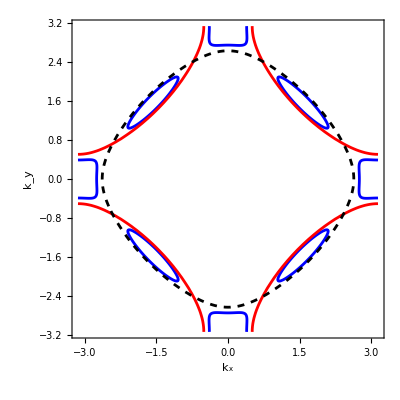

doping p:

-5.98412×10^-6

ρ_c:

0.500003

ρ_f:

0.500003

```mathematica
μc=-0.448;
tc=1;
tc1=-0.2;
tc2=0;
tc3=0;
c=4;
L=48;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.25;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;
Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]]
T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

```mathematica
78820./3600//N
```

21.8944

```mathematica
L=21;
data=SortBy[Flatten[Table[{{kx,ky,E1},{kx,ky,E2}},{kx,-π,π-2 π/L,(2π)/L},{ky,-π,π-2 π/L,(2π)/L}],2],Last];
data[[L^2-1;;L^2+3]]
```

{{(13 π)/21,-(3 π)/7,0.00337088},{(13 π)/21,(3 π)/7,0.00337088},{-(19 π)/21,-π/7,0.0320589},{-(19 π)/21,π/7,0.0320589},{-π/7,-(19 π)/21,0.0320589}}

{π/8,-(23 π)/24,-0.0495969}

```mathematica
data[[L^2-1;;L^2+1]]
```

{{π/24,-(7 π)/8,-0.000596934},{π/24,(7 π)/8,-0.000596934},{π/8,-(23 π)/24,-0.000596934}}

ground state(N=1/2)

```mathematica
L=23;
data=SortBy[Flatten[Table[{{kx,ky,E1},{kx,ky,E2}},{kx,-π,π-2 π/L,(2π)/L},{ky,-π,π-2 π/L,(2π)/L}],2],Last];
occupied=data[[1;;L^2]];
empty=Complement[data,occupied];

{Kx0,Ky0,En0}=Total[occupied]
```

{-25 π,-25 π,-646.822}

ground state(N=1/2+1)

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];

{Kx1,Ky1,En1}=Total[occupied1]
```

{-26 π,-(578 π)/23,-646.808}

{-π/6,-(5 π)/6,0.05}

Excited state(N=1/2+1)

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[Kx1-occupied1[[i]][[1]]+empty1[[j]][[1]]-Kx0,2π],Mod[Ky1-occupied1[[i]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2-20,L^2+1},{j,1,L^2-1}],1];
exc=SortBy[exc,Last];
```

```mathematica
exc=ParallelTable[{Mod[empty[[i]][[1]],2π],Mod[empty[[i]][[2]],2π],empty[[i]][[3]]}

,{i,1,L^2}];
exc=SortBy[exc,Last];
```

```mathematica
exc
```

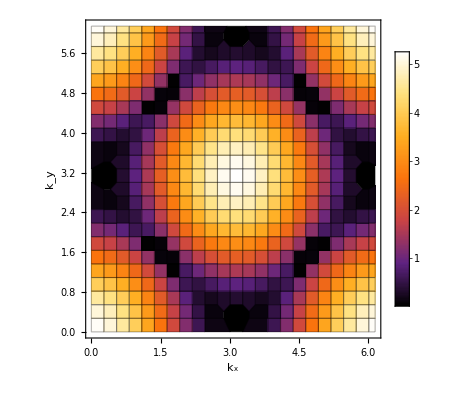

```mathematica
ListDensityPlot[exc,PlotRange->{0,6},ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
```

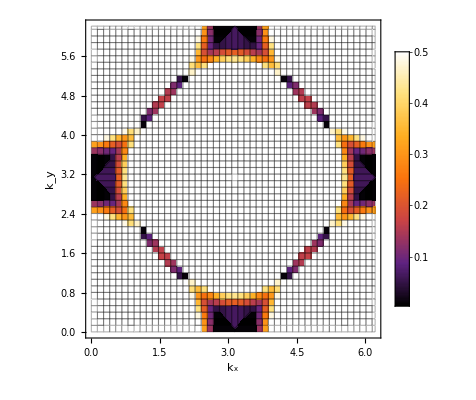
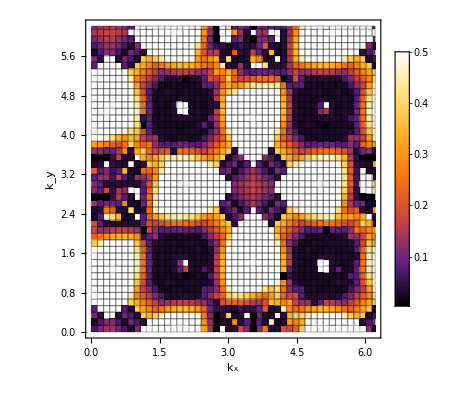

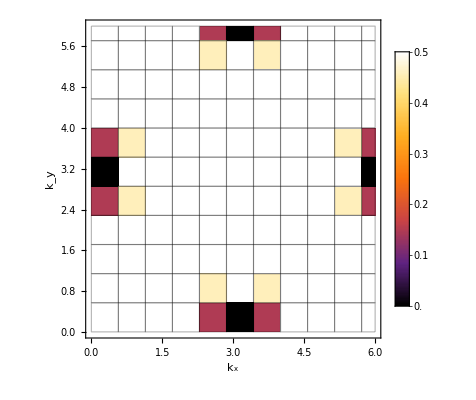
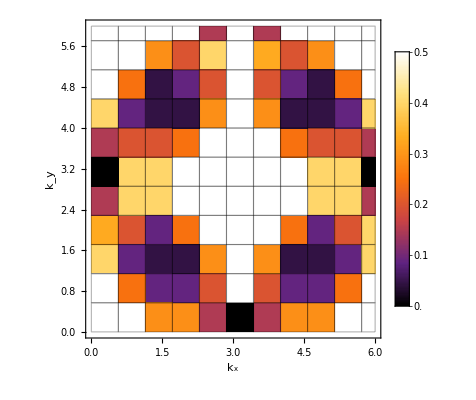

```mathematica
ListDensityPlot[exc,PlotRange->{0,0.5},ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
```

-Graphics-

```mathematica
|
```

```mathematica
exc[[1;;50]]
```

{{(3 π)/47,(41 π)/47,0.00295437},{(3 π)/47,(53 π)/47,0.00295437},{(41 π)/47,(3 π)/47,0.00295437},{(41 π)/47,(91 π)/47,0.00295437},{(53 π)/47,(3 π)/47,0.00295437},{(53 π)/47,(91 π)/47,0.00295437},{(91 π)/47,(41 π)/47,0.00295437},{(91 π)/47,(53 π)/47,0.00295437},{(5 π)/47,(41 π)/47,0.00680595},{(5 π)/47,(53 π)/47,0.00680595},{(41 π)/47,(5 π)/47,0.00680595},{(41 π)/47,(89 π)/47,0.00680595},{(53 π)/47,(5 π)/47,0.00680595},{(53 π)/47,(89 π)/47,0.00680595},{(89 π)/47,(41 π)/47,0.00680595},{(89 π)/47,(53 π)/47,0.00680595},{π/47,(41 π)/47,0.00687323},{π/47,(53 π)/47,0.00687323},{(41 π)/47,π/47,0.00687323},{(41 π)/47,(93 π)/47,0.00687323},{(53 π)/47,π/47,0.00687323},{(53 π)/47,(93 π)/47,0.00687323},{(93 π)/47,(41 π)/47,0.00687323},{(93 π)/47,(53 π)/47,0.00687323},{(17 π)/47,(31 π)/47,0.00916144},{(17 π)/47,(63 π)/47,0.00916144},{(31 π)/47,(17 π)/47,0.00916144},{(31 π)/47,(77 π)/47,0.00916144},{(63 π)/47,(17 π)/47,0.00916144},{(63 π)/47,(77 π)/47,0.00916144},{(77 π)/47,(31 π)/47,0.00916144},{(77 π)/47,(63 π)/47,0.00916144},{(7 π)/47,(41 π)/47,0.0468948},{(7 π)/47,(53 π)/47,0.0468948},{(41 π)/47,(7 π)/47,0.0468948},{(41 π)/47,(87 π)/47,0.0468948},{(53 π)/47,(7 π)/47,0.0468948},{(53 π)/47,(87 π)/47,0.0468948},{(87 π)/47,(41 π)/47,0.0468948},{(87 π)/47,(53 π)/47,0.0468948},{(7 π)/47,(43 π)/47,0.0478114},{(7 π)/47,(51 π)/47,0.0478114},{(43 π)/47,(7 π)/47,0.0478114},{(43 π)/47,(87 π)/47,0.0478114},{(51 π)/47,(7 π)/47,0.0478114},{(51 π)/47,(87 π)/47,0.0478114},{(87 π)/47,(43 π)/47,0.0478114},{(87 π)/47,(51 π)/47,0.0478114},{(17 π)/47,(29 π)/47,0.0483266},{(17 π)/47,(65 π)/47,0.0483266}}

```mathematica
exc[[1;;50]]
```

{{(3 π)/47,(41 π)/47,0.00295437},{(3 π)/47,(53 π)/47,0.00295437},{(41 π)/47,(3 π)/47,0.00295437},{(41 π)/47,(91 π)/47,0.00295437},{(53 π)/47,(3 π)/47,0.00295437},{(91 π)/47,(41 π)/47,0.00295437},{(91 π)/47,(53 π)/47,0.00295437},{(5 π)/47,(41 π)/47,0.00680595},{(5 π)/47,(53 π)/47,0.00680595},{(41 π)/47,(5 π)/47,0.00680595},{(41 π)/47,(89 π)/47,0.00680595},{(53 π)/47,(5 π)/47,0.00680595},{(53 π)/47,(89 π)/47,0.00680595},{(89 π)/47,(41 π)/47,0.00680595},{(89 π)/47,(53 π)/47,0.00680595},{π/47,(41 π)/47,0.00687323},{π/47,(53 π)/47,0.00687323},{(41 π)/47,π/47,0.00687323},{(41 π)/47,(93 π)/47,0.00687323},{(53 π)/47,π/47,0.00687323},{(53 π)/47,(93 π)/47,0.00687323},{(93 π)/47,(41 π)/47,0.00687323},{(93 π)/47,(53 π)/47,0.00687323},{(17 π)/47,(31 π)/47,0.00916144},{(17 π)/47,(63 π)/47,0.00916144},{(31 π)/47,(17 π)/47,0.00916144},{(31 π)/47,(77 π)/47,0.00916144},{(63 π)/47,(17 π)/47,0.00916144},{(63 π)/47,(77 π)/47,0.00916144},{(77 π)/47,(31 π)/47,0.00916144},{(77 π)/47,(63 π)/47,0.00916144},{(25 π)/47,(13 π)/47,0.0219171},{(25 π)/47,(25 π)/47,0.0219171},{(31 π)/47,(13 π)/47,0.0219171},{(31 π)/47,(25 π)/47,0.0219171},{(69 π)/47,(63 π)/47,0.0219171},{(69 π)/47,(69 π)/47,0.0219171},{(81 π)/47,(69 π)/47,0.0219171},{(23 π)/47,(13 π)/47,0.0257687},{(23 π)/47,(25 π)/47,0.0257687},{(33 π)/47,(13 π)/47,0.0257687},{(33 π)/47,(25 π)/47,0.0257687},{(69 π)/47,(61 π)/47,0.0257687},{(69 π)/47,(71 π)/47,0.0257687},{(81 π)/47,(61 π)/47,0.0257687},{(81 π)/47,(71 π)/47,0.0257687},{(27 π)/47,(13 π)/47,0.025836},{(27 π)/47,(25 π)/47,0.025836},{(29 π)/47,(13 π)/47,0.025836},{(29 π)/47,(25 π)/47,0.025836}}

```mathematica
data[[1;;L^2]]
```

{{-π,-π,-2.8078},{0,0,-2.8078},{0,-π/6,-2.64759},{0,π/6,-2.64759},{-π,-(5 π)/6,-2.64759},{-π,(5 π)/6,-2.64759},{-(5 π)/6,-π,-2.64759},{-π/6,0,-2.64759},{π/6,0,-2.64759},{(5 π)/6,-π,-2.64759},{-(5 π)/6,-(5 π)/6,-2.47311},{-(5 π)/6,(5 π)/6,-2.47311},{-π/6,-π/6,-2.47311},{-π/6,π/6,-2.47311},{π/6,-π/6,-2.47311},{π/6,π/6,-2.47311},{(5 π)/6,-(5 π)/6,-2.47311},{(5 π)/6,(5 π)/6,-2.47311},{0,-π/3,-2.2104},{0,π/3,-2.2104},{-π,-(2 π)/3,-2.2104},{-π,(2 π)/3,-2.2104},{-(2 π)/3,-π,-2.2104},{-π/3,0,-2.2104},{π/3,0,-2.2104},{(2 π)/3,-π,-2.2104},{-(5 π)/6,-(2 π)/3,-1.99706},{-(5 π)/6,(2 π)/3,-1.99706},{-(2 π)/3,-(5 π)/6,-1.99706},{-(2 π)/3,(5 π)/6,-1.99706},{-π/3,-π/6,-1.99706},{-π/3,π/6,-1.99706},{-π/6,-π/3,-1.99706},{-π/6,π/3,-1.99706},{π/6,-π/3,-1.99706},{π/6,π/3,-1.99706},{π/3,-π/6,-1.99706},{π/3,π/6,-1.99706},{(2 π)/3,-(5 π)/6,-1.99706},{(2 π)/3,(5 π)/6,-1.99706},{(5 π)/6,-(2 π)/3,-1.99706},{(5 π)/6,(2 π)/3,-1.99706},{0,-π/2,-1.61556},{0,π/2,-1.61556},{-π,-π/2,-1.61556},{-π,π/2,-1.61556},{-π/2,0,-1.61556},{-π/2,-π,-1.61556},{π/2,0,-1.61556},{π/2,-π,-1.61556},{-π/3,-π/3,-1.41556},{-π/3,π/3,-1.41556},{π/3,-π/3,-1.41556},{π/3,π/3,-1.41556},{-(2 π)/3,-(2 π)/3,-1.41556},{-(2 π)/3,(2 π)/3,-1.41556},{(2 π)/3,-(2 π)/3,-1.41556},{(2 π)/3,(2 π)/3,-1.41556},{-(5 π)/6,-π/2,-1.35},{-(5 π)/6,π/2,-1.35},{-π/2,-(5 π)/6,-1.35},{-π/2,-π/6,-1.35},{-π/2,π/6,-1.35},{-π/2,(5 π)/6,-1.35},{-π/6,-π/2,-1.35},{-π/6,π/2,-1.35},{π/6,-π/2,-1.35},{π/6,π/2,-1.35},{π/2,-(5 π)/6,-1.35},{π/2,-π/6,-1.35},{π/2,π/6,-1.35},{π/2,(5 π)/6,-1.35},{(5 π)/6,-π/2,-1.35},{(5 π)/6,π/2,-1.35},{0,-(2 π)/3,-1.03078},{0,(2 π)/3,-1.03078},{-π,-π/3,-1.03078},{-π,π/3,-1.03078},{-(2 π)/3,0,-1.03078},{-π/3,-π,-1.03078},{π/3,-π,-1.03078},{(2 π)/3,0,-1.03078},{-(5 π)/6,-π/3,-0.719972},{-(5 π)/6,π/3,-0.719972},{-(2 π)/3,-π/6,-0.719972},{-(2 π)/3,π/6,-0.719972},{-π/3,-(5 π)/6,-0.719972},{-π/3,(5 π)/6,-0.719972},{-π/6,-(2 π)/3,-0.719972},{-π/6,(2 π)/3,-0.719972},{π/6,-(2 π)/3,-0.719972},{π/6,(2 π)/3,-0.719972},{π/3,-(5 π)/6,-0.719972},{π/3,(5 π)/6,-0.719972},{(2 π)/3,-π/6,-0.719972},{(2 π)/3,π/6,-0.719972},{(5 π)/6,-π/3,-0.719972},{(5 π)/6,π/3,-0.719972},{0,-(5 π)/6,-0.659286},{0,(5 π)/6,-0.659286},{-π,-π/6,-0.659286},{-π,π/6,-0.659286},{-(5 π)/6,0,-0.659286},{-π/6,-π,-0.659286},{π/6,-π,-0.659286},{(5 π)/6,0,-0.659286},{0,-π,-0.65},{-π,0,-0.65},{-(2 π)/3,-π/2,-0.630776},{-(2 π)/3,π/2,-0.630776},{-π/2,-(2 π)/3,-0.630776},{-π/2,-π/3,-0.630776},{-π/2,π/3,-0.630776},{-π/2,(2 π)/3,-0.630776},{-π/3,-π/2,-0.630776},{-π/3,π/2,-0.630776},{π/3,-π/2,-0.630776},{π/3,π/2,-0.630776},{π/2,-(2 π)/3,-0.630776},{π/2,-π/3,-0.630776},{π/2,π/3,-0.630776},{π/2,(2 π)/3,-0.630776},{(2 π)/3,-π/2,-0.630776},{(2 π)/3,π/2,-0.630776},{-(5 π)/6,-π/6,-0.45},{-(5 π)/6,π/6,-0.45},{-π/6,-(5 π)/6,-0.45},{-π/6,(5 π)/6,-0.45},{π/6,-(5 π)/6,-0.45},{π/6,(5 π)/6,-0.45},{(5 π)/6,-π/6,-0.45},{(5 π)/6,π/6,-0.45},{0,-π,-0.15},{-π,0,-0.15},{-(2 π)/3,-π/3,-0.05},{-(2 π)/3,π/3,-0.05},{-π/3,-(2 π)/3,-0.05},{-π/3,(2 π)/3,-0.05},{π/3,-(2 π)/3,-0.05},{π/3,(2 π)/3,-0.05},{(2 π)/3,-π/3,-0.05},{(2 π)/3,π/3,-0.05},{-(5 π)/6,-π/6,0.05},{-(5 π)/6,π/6,0.05}}

```mathematica
data[[1;;L^2+2]]
```

{{-π,-π,-2.8078},{0,0,-2.8078},{0,-π/6,-2.64759},{0,π/6,-2.64759},{-π,-(5 π)/6,-2.64759},{-π,(5 π)/6,-2.64759},{-(5 π)/6,-π,-2.64759},{-π/6,0,-2.64759},{π/6,0,-2.64759},{(5 π)/6,-π,-2.64759},{-(5 π)/6,-(5 π)/6,-2.47311},{-(5 π)/6,(5 π)/6,-2.47311},{-π/6,-π/6,-2.47311},{-π/6,π/6,-2.47311},{π/6,-π/6,-2.47311},{π/6,π/6,-2.47311},{(5 π)/6,-(5 π)/6,-2.47311},{(5 π)/6,(5 π)/6,-2.47311},{0,-π/3,-2.2104},{0,π/3,-2.2104},{-π,-(2 π)/3,-2.2104},{-π,(2 π)/3,-2.2104},{-(2 π)/3,-π,-2.2104},{-π/3,0,-2.2104},{π/3,0,-2.2104},{(2 π)/3,-π,-2.2104},{-(5 π)/6,-(2 π)/3,-1.99706},{-(5 π)/6,(2 π)/3,-1.99706},{-(2 π)/3,-(5 π)/6,-1.99706},{-(2 π)/3,(5 π)/6,-1.99706},{-π/3,-π/6,-1.99706},{-π/3,π/6,-1.99706},{-π/6,-π/3,-1.99706},{-π/6,π/3,-1.99706},{π/6,-π/3,-1.99706},{π/6,π/3,-1.99706},{π/3,-π/6,-1.99706},{π/3,π/6,-1.99706},{(2 π)/3,-(5 π)/6,-1.99706},{(2 π)/3,(5 π)/6,-1.99706},{(5 π)/6,-(2 π)/3,-1.99706},{(5 π)/6,(2 π)/3,-1.99706},{0,-π/2,-1.61556},{0,π/2,-1.61556},{-π,-π/2,-1.61556},{-π,π/2,-1.61556},{-π/2,0,-1.61556},{-π/2,-π,-1.61556},{π/2,0,-1.61556},{π/2,-π,-1.61556},{-π/3,-π/3,-1.41556},{-π/3,π/3,-1.41556},{π/3,-π/3,-1.41556},{π/3,π/3,-1.41556},{-(2 π)/3,-(2 π)/3,-1.41556},{-(2 π)/3,(2 π)/3,-1.41556},{(2 π)/3,-(2 π)/3,-1.41556},{(2 π)/3,(2 π)/3,-1.41556},{-(5 π)/6,-π/2,-1.35},{-(5 π)/6,π/2,-1.35},{-π/2,-(5 π)/6,-1.35},{-π/2,-π/6,-1.35},{-π/2,π/6,-1.35},{-π/2,(5 π)/6,-1.35},{-π/6,-π/2,-1.35},{-π/6,π/2,-1.35},{π/6,-π/2,-1.35},{π/6,π/2,-1.35},{π/2,-(5 π)/6,-1.35},{π/2,-π/6,-1.35},{π/2,π/6,-1.35},{π/2,(5 π)/6,-1.35},{(5 π)/6,-π/2,-1.35},{(5 π)/6,π/2,-1.35},{0,-(2 π)/3,-1.03078},{0,(2 π)/3,-1.03078},{-π,-π/3,-1.03078},{-π,π/3,-1.03078},{-(2 π)/3,0,-1.03078},{-π/3,-π,-1.03078},{π/3,-π,-1.03078},{(2 π)/3,0,-1.03078},{-(5 π)/6,-π/3,-0.719972},{-(5 π)/6,π/3,-0.719972},{-(2 π)/3,-π/6,-0.719972},{-(2 π)/3,π/6,-0.719972},{-π/3,-(5 π)/6,-0.719972},{-π/3,(5 π)/6,-0.719972},{-π/6,-(2 π)/3,-0.719972},{-π/6,(2 π)/3,-0.719972},{π/6,-(2 π)/3,-0.719972},{π/6,(2 π)/3,-0.719972},{π/3,-(5 π)/6,-0.719972},{π/3,(5 π)/6,-0.719972},{(2 π)/3,-π/6,-0.719972},{(2 π)/3,π/6,-0.719972},{(5 π)/6,-π/3,-0.719972},{(5 π)/6,π/3,-0.719972},{0,-(5 π)/6,-0.659286},{0,(5 π)/6,-0.659286},{-π,-π/6,-0.659286},{-π,π/6,-0.659286},{-(5 π)/6,0,-0.659286},{-π/6,-π,-0.659286},{π/6,-π,-0.659286},{(5 π)/6,0,-0.659286},{0,-π,-0.65},{-π,0,-0.65},{-(2 π)/3,-π/2,-0.630776},{-(2 π)/3,π/2,-0.630776},{-π/2,-(2 π)/3,-0.630776},{-π/2,-π/3,-0.630776},{-π/2,π/3,-0.630776},{-π/2,(2 π)/3,-0.630776},{-π/3,-π/2,-0.630776},{-π/3,π/2,-0.630776},{π/3,-π/2,-0.630776},{π/3,π/2,-0.630776},{π/2,-(2 π)/3,-0.630776},{π/2,-π/3,-0.630776},{π/2,π/3,-0.630776},{π/2,(2 π)/3,-0.630776},{(2 π)/3,-π/2,-0.630776},{(2 π)/3,π/2,-0.630776},{-(5 π)/6,-π/6,-0.45},{-(5 π)/6,π/6,-0.45},{-π/6,-(5 π)/6,-0.45},{-π/6,(5 π)/6,-0.45},{π/6,-(5 π)/6,-0.45},{π/6,(5 π)/6,-0.45},{(5 π)/6,-π/6,-0.45},{(5 π)/6,π/6,-0.45},{0,-π,-0.15},{-π,0,-0.15},{-(2 π)/3,-π/3,-0.05},{-(2 π)/3,π/3,-0.05},{-π/3,-(2 π)/3,-0.05},{-π/3,(2 π)/3,-0.05},{π/3,-(2 π)/3,-0.05},{π/3,(2 π)/3,-0.05},{(2 π)/3,-π/3,-0.05},{(2 π)/3,π/3,-0.05},{-(5 π)/6,-π/6,0.05},{-(5 π)/6,π/6,0.05},{-π/6,-(5 π)/6,0.05},{-π/6,(5 π)/6,0.05}}

```mathematica
|
```

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[Kx1-occupied1[[i]][[1]]+empty1[[j]][[1]]-Kx0,2π],Mod[Ky1-occupied1[[i]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2,L^2+1},{j,L^2+1-100,L^2-1}],1];
exc=SortBy[exc,Last];
exc[[1;;50]]
```

{{π/6,(5 π)/6,0.05},{π/6,(7 π)/6,0.05},{π/2,(11 π)/6,0.05},{(5 π)/6,π/6,0.05},{(5 π)/6,π/6,0.05},{(5 π)/6,(11 π)/6,0.05},{(5 π)/6,(11 π)/6,0.05},{(3 π)/2,(5 π)/6,0.05},{(3 π)/2,(7 π)/6,0.05},{(11 π)/6,(5 π)/6,0.05},{π/6,π,0.0736449},{π/2,0,0.0736449},{(5 π)/6,0,0.0736449},{(5 π)/6,0,0.0736449},{(3 π)/2,π,0.0736449},{(11 π)/6,π,0.0736449},{π/6,π/2,0.15},{π/6,(3 π)/2,0.15},{π/2,π/2,0.15},{π/2,(3 π)/2,0.15},{(7 π)/6,π/2,0.15},{(7 π)/6,(3 π)/2,0.15},{(3 π)/2,π/2,0.15},{(3 π)/2,(3 π)/2,0.15},{π/3,π/3,0.45},{π/3,(2 π)/3,0.45},{π/3,(4 π)/3,0.45},{π/3,(5 π)/3,0.45},{(2 π)/3,π/3,0.45},{(2 π)/3,(5 π)/3,0.45},{π,π/3,0.45},{π,(5 π)/3,0.45},{(4 π)/3,(2 π)/3,0.45},{(4 π)/3,(4 π)/3,0.45},{(5 π)/3,(2 π)/3,0.45},{(5 π)/3,(4 π)/3,0.45},{π/6,π/2,0.65},{π/6,(3 π)/2,0.65},{π/2,π/2,0.65},{π/2,(3 π)/2,0.65},{(7 π)/6,π/2,0.65},{(7 π)/6,(3 π)/2,0.65},{(3 π)/2,π/2,0.65},{(3 π)/2,(3 π)/2,0.65},{π/6,(2 π)/3,0.827152},{π/6,(4 π)/3,0.827152},{π/3,π/6,0.827152},{π/3,(5 π)/6,0.827152},{π/3,(7 π)/6,0.827152},{π/3,(11 π)/6,0.827152}}

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[+empty1[[j]][[1]],2π],Mod[Ky1-occupied1[[j]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2+1,L^2+1},{j,L^2+1-100,L^2-1}],1];
exc=SortBy[exc,Last];
exc[[1;;50]]
```

{{π/6,0,0.05},{π/6,(5 π)/6,0.05},{(5 π)/6,0,0.05},{(5 π)/6,π/3,0.05},{(11 π)/6,π,0.05},{π/6,π/2,0.0736449},{(5 π)/6,π,0.0736449},{(11 π)/6,(4 π)/3,0.0736449},{π/2,π/6,0.15},{π/2,(7 π)/6,0.15},{(3 π)/2,π/3,0.15},{(3 π)/2,(2 π)/3,0.15},{π/3,(5 π)/6,0.45},{π/3,(5 π)/6,0.45},{(2 π)/3,(2 π)/3,0.45},{(2 π)/3,π,0.45},{(5 π)/3,(2 π)/3,0.45},{(5 π)/3,(2 π)/3,0.45},{π/2,π/6,0.65},{π/2,(4 π)/3,0.65},{(3 π)/2,π,0.65},{(3 π)/2,(5 π)/3,0.65},{π/6,(2 π)/3,0.827152},{π/6,(7 π)/6,0.827152},{π/3,π/6,0.827152},{π/3,π,0.827152},{(2 π)/3,π/6,0.827152},{(2 π)/3,(5 π)/6,0.827152},{(5 π)/6,(5 π)/6,0.827152},{(5 π)/6,(3 π)/2,0.827152},{(5 π)/3,π/6,0.827152},{(5 π)/3,(7 π)/6,0.827152},{(11 π)/6,(5 π)/6,0.827152},{(11 π)/6,π,0.827152},{π/3,π/3,1.03078},{(2 π)/3,(3 π)/2,1.03078},{(5 π)/3,(5 π)/3,1.03078},{π/3,π/3,1.43078},{π/3,(5 π)/3,1.43078},{π/2,0,1.43078},{π/2,π,1.43078},{π/2,(7 π)/6,1.43078},{π/2,(4 π)/3,1.43078},{(2 π)/3,π/6,1.43078},{(2 π)/3,π/2,1.43078},{(3 π)/2,π/2,1.43078},{(3 π)/2,(7 π)/6,1.43078},{(3 π)/2,(7 π)/6,1.43078},{(3 π)/2,(3 π)/2,1.43078},{(5 π)/3,π/2,1.43078}}